```mathematica
Clear["Global`*"]
```

## Part A

```mathematica
L=20;
V[x_]:= -Sech[x]^2/; Abs[x]≤L/2
```

```mathematica
V[x_]:= 0/;Abs[x]>L/2
```

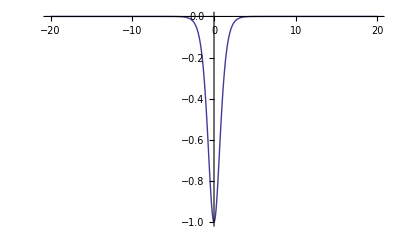

```mathematica
Plot[V[x],{x,-L,L},PlotRange->All]
```

```mathematica
Part B
```

B Part

```mathematica
B = 1;
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(en = energy; NDSolve[{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], 
					ψ2'[-L/2] ==  ψ1'[-L/2]}, 
		ψ2, {x, -L/2, 0} ])
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A=B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -1, 0} ]
```

-0.5

Energy ground state = -15.32

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0
```

```mathematica
ψnn[x_] := ψ1[x] /; x < -L/2
```

```mathematica
ψnn [x_] := ψ3[x] /; x > L/2
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

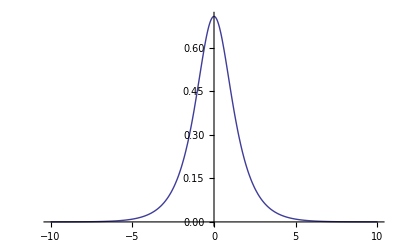

```mathematica
Plot[ψ[x],{x,-L/2,L/2},PlotRange->All]
```

```mathematica
Part C
```

```mathematica
ψknown[x_]:= (1/Sqrt[2])Sech[x]
```

```mathematica
V[x_]:= -Sech[x]^2
```

```mathematica
eqn[en_] := ψknown''[x] + 2(en - V[en])ψknown[x]
```

```mathematica
energy[x_]=Solve[eqn[en]==0,x][[1]];
```

```mathematica
en/.energy[0][[1]]
```

-0.5

Which is what we calculated before numerically